```mathematica
selectnD[conds_,n_]:=Select[conds,RegionDimension[ImplicitRegion[#,{a′,γ′}]]==n&]
```

```mathematica
seperateOr[conds_]:=If[Head[LogicalExpand[conds]]===Or,List@@LogicalExpand[conds],{LogicalExpand[conds]}]
```

```mathematica
rules = Table[DeleteCases[Reduce[Simplify[Reduce[Simplify[#,assumptions′]],assumptions′]]&/@seperateOr[e[[3]]],False],{e,eq}];
rules0D = Table[selectnD[r,0],{r,rules}];
rules1D = Table[selectnD[r,1],{r,rules}];
rules2D = Table[selectnD[r,2],{r,rules}];
```

```mathematica
Flatten[DeleteCases[(selectnD[#,0]&/@rules)//N,{}]]//DeleteDuplicates//Length
```

7

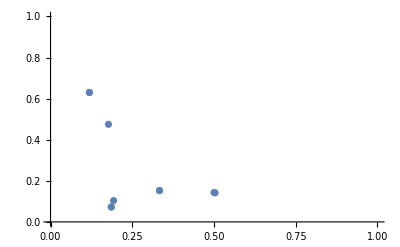

```mathematica
ListPlot[{#[[1,2]],#[[2,2]]}&/@Flatten[DeleteCases[rules0D//N,{}]],PlotRange->{{0,1},{0,1}}]
```

```mathematica
rules0D//N//MatrixForm
rules1D//N//MatrixForm
```

({γ′==0.118955&&a′==0.630076}
{a′==0.50341&&γ′==0.141495}
{a′==0.192792&&γ′==0.103604,a′==0.177164&&γ′==0.475037}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{γ′==0.118955&&a′==0.630076}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{a′==0.5&&γ′==0.142857})

({}
{}
{}
{γ′≤0.0837078&&a′==-(2. γ′)/(-1.+3. γ′)}
{}
{}
{γ′≤0.0837078&&a′==-(2. γ′)/(-1.+3. γ′)}
{}
{})

```mathematica
Table[(eq/.r)//MatrixForm,{r,(Solve[#,{a′,γ′}][[1]]&/@(rules0D//N//Flatten))}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{({2,8} | {2.40958,1.} | True
{5,5} | {1.99996,1.99996} | False
{6,6} | {1.86779,1.86779} | False
{6,8} | {2.11678,0.916344} | False
{7,8} | {3.23356,0.832688} | False
{8,2} | {1.,2.40958} | True
{8,6} | {0.916344,2.11678} | False
{8,7} | {0.832688,3.23356} | False
{8,8} | {1,1} | True),({2,8} | {2.7775,0.997194} | False
{5,5} | {1.89901,1.89901} | True
{6,6} | {1.76557,1.76557} | False
{6,8} | {1.89901,0.996635} | False
{7,8} | {2.79802,0.993269} | False
{8,2} | {0.997194,2.7775} | False
{8,6} | {0.996635,1.89901} | False
{8,7} | {0.993269,2.79802} | False
{8,8} | {1,1} | True),({2,8} | {3.85063,0.65089} | False
{5,5} | {1.47503,1.47503} | True
{6,6} | {1.41928,1.41928} | True
{6,8} | {1.41928,1.03717} | False
{7,8} | {1.83856,1.07434} | False
{8,2} | {0.65089,3.85063} | False
{8,6} | {1.03717,1.41928} | False
{8,7} | {1.07434,1.83856} | False
{8,8} | {1,1} | False),({2,8} | {2.50528,2.29987} | False
{5,5} | {2.09504,2.09504} | False
{6,6} | {1.98427,1.98427} | True
{6,8} | {1.53481,1.51269} | False
{7,8} | {2.06961,2.02539} | False
{8,2} | {2.29987,2.50528} | False
{8,6} | {1.51269,1.53481} | False
{8,7} | {2.02539,2.06961} | False
{8,8} | {1,1} | False),({2,8} | {3.98804,0.508561} | False
{5,5} | {1.41097,1.41097} | True
{6,6} | {1.36578,1.36578} | False
{6,8} | {1.397,1.} | True
{7,8} | {1.79401,1.} | True
{8,2} | {0.508561,3.98804} | False
{8,6} | {1.,1.397} | True
{8,7} | {1.,1.79401} | True
{8,8} | {1,1} | True),({2,8} | {3.07906,1.66667} | False
{5,5} | {1.82853,1.82853} | False
{6,6} | {1.74744,1.74744} | True
{6,8} | {1.46047,1.33333} | False
{7,8} | {1.92094,1.66667} | True
{8,2} | {1.66667,3.07906} | False
{8,6} | {1.33333,1.46047} | False
{8,7} | {1.66667,1.92094} | True
{8,8} | {1,1} | False),({2,8} | {2.40958,1.} | True
{5,5} | {1.99996,1.99996} | False
{6,6} | {1.86779,1.86779} | False
{6,8} | {2.11678,0.916344} | False
{7,8} | {3.23356,0.832688} | False
{8,2} | {1.,2.40958} | True
{8,6} | {0.916344,2.11678} | False
{8,7} | {0.832688,3.23356} | False
{8,8} | {1,1} | True),({2,8} | {3.98804,0.508561} | False
{5,5} | {1.41097,1.41097} | True
{6,6} | {1.36578,1.36578} | False
{6,8} | {1.397,1.} | True
{7,8} | {1.79401,1.} | True
{8,2} | {0.508561,3.98804} | False
{8,6} | {1.,1.397} | True
{8,7} | {1.,1.79401} | True
{8,8} | {1,1} | True),({2,8} | {3.07906,1.66667} | False
{5,5} | {1.82853,1.82853} | False
{6,6} | {1.74744,1.74744} | True
{6,8} | {1.46047,1.33333} | False
{7,8} | {1.92094,1.66667} | True
{8,2} | {1.66667,3.07906} | False
{8,6} | {1.33333,1.46047} | False
{8,7} | {1.66667,1.92094} | True
{8,8} | {1,1} | False),({2,8} | {2.78571,1.} | False
{5,5} | {1.89717,1.89717} | True
{6,6} | {1.76354,1.76354} | False
{6,8} | {1.89286,1.} | False
{7,8} | {2.78571,1.} | False
{8,2} | {1.,2.78571} | False
{8,6} | {1.,1.89286} | False
{8,7} | {1.,2.78571} | False
{8,8} | {1,1} | True)}

```mathematica
OneD = Simplify[Solve[rules1D[[4]],{a′,γ′}],assumptions′]//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a′→ConditionalExpression[(2. γ′)/(1.-3. γ′), γ′≤0.0837078]}}

```mathematica
(eq[[;;,3]]/.OneD[[1]])
```

{ConditionalExpression[((2. γ′)/(1.-3. γ′)==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&γ′+AlgebraicNumber-0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 γ′≤1&&((6. γ′)/(1.-3. γ′)≥5||((2. γ′)/(1.-3. γ′)>Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+(6. γ′^2)/(1.-3. γ′)≤5 γ′+(2. γ′)/(1.-3. γ′))))||((-1+(2. γ′)/(1.-3. γ′))/(-5+(6. γ′)/(1.-3. γ′))≤γ′&&(((2. γ′)/(1.-3. γ′)>Root0.630Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&(2. γ′)/(1.-3. γ′)≤Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&γ′+(2. γ′ (-10+(2. γ′)/(1.-3. γ′)+(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (5-(14. γ′)/(1.-3. γ′))^2)+24. √((γ′^3 (5-(20. γ′)/(1.-3. γ′)+(16. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (5-(14. γ′)/(1.-3. γ′))^4))≤0)||((2. γ′)/(1.-3. γ′)>Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(2. γ′)/(1.-3. γ′)≤Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&γ′+16. √((γ′^2 (32-(184. γ′)/(1.-3. γ′)+(448. γ′^2)/(1.-3. γ′)^2-(600. γ′^3)/(1.-3. γ′)^3+(368. γ′^4)/(1.-3. γ′)^4))/((1.-3. γ′)^2 (8-(14. γ′)/(1.-3. γ′))^4))≤(32-(120. γ′)/(1.-3. γ′)+(272. γ′^2)/(1.-3. γ′)^2-(312. γ′^3)/(1.-3. γ′)^3)/(8-(14. γ′)/(1.-3. γ′))^2))), γ′≤0.0837078],ConditionalExpression[(2+(6. γ′)/(1.-3. γ′)==0&&54 γ′≤17+√145)||((2. γ′)/(1.-3. γ′)==Root-0.590Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324&&γ′==1/72 ((-24+(24. γ′)/(1.-3. γ′)-(52. γ′^2)/(1.-3. γ′)^2)/(-1+(2. γ′)/(1.-3. γ′))+10. √((γ′^2 (48-(48. γ′)/(1.-3. γ′)+(4. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′)^2 (-1+(2. γ′)/(1.-3. γ′))^2))))||((2. γ′)/(1.-3. γ′)==Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&6916252 γ′+3 √(7 (351156463431424-5958129102912 Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694-68154041956 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^2+225248900 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^3+13811831 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^4))==1372 (101154-131684 Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259-248261 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^2+28136 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^3+432572 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^4))||(1/2 ((2. γ′ (4+(18. γ′)/(1.-3. γ′)+(8. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2+(6. γ′)/(1.-3. γ′))^2)-2.82843 √(-(γ′^3 (-8-(18. γ′)/(1.-3. γ′)+(48. γ′^2)/(1.-3. γ′)^2+(40. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2+(6. γ′)/(1.-3. γ′))^4)))≤γ′&&((γ′≤1/72 ((-24+(24. γ′)/(1.-3. γ′)-(52. γ′^2)/(1.-3. γ′)^2)/(-1+(2. γ′)/(1.-3. γ′))+10. √((γ′^2 (48-(48. γ′)/(1.-3. γ′)+(4. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′)^2 (-1+(2. γ′)/(1.-3. γ′))^2)))&&(-2/3<(2. γ′)/(1.-3. γ′)<Root-0.590Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324||(2+(6. γ′)/(1.-3. γ′)<0&&17+√129+(20. γ′)/(1.-3. γ′)≥0)))||((2. γ′)/(1.-3. γ′)>Root0.477Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&(2. γ′)/(1.-3. γ′)<Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&γ′+3. √((γ′^2 (8-(16. γ′)/(1.-3. γ′)-(20. γ′^2)/(1.-3. γ′)^2-(80. γ′^3)/(1.-3. γ′)^3+(240. γ′^4)/(1.-3. γ′)^4))/((1.-3. γ′)^2 (1+(2. γ′)/(1.-3. γ′))^4))≤(2+(4. γ′^2)/(1.-3. γ′)^2-(48. γ′^3)/(1.-3. γ′)^3)/(1+(2. γ′)/(1.-3. γ′))^2)||(0≤(2. γ′)/(1.-3. γ′)&&(2. γ′)/(1.-3. γ′)≤Root0.477Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&γ′≤1/72 ((-24+(24. γ′)/(1.-3. γ′)-(52. γ′^2)/(1.-3. γ′)^2)/(-1+(2. γ′)/(1.-3. γ′))-10. √((γ′^2 (48-(48. γ′)/(1.-3. γ′)+(4. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′)^2 (-1+(2. γ′)/(1.-3. γ′))^2)))))), γ′≤0.0837078],ConditionalExpression[((2. γ′)/(1.-3. γ′)==0&&0≤γ′&&3 γ′≤1)||((2. γ′)/(1.-3. γ′)==Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&2520 γ′==952+√(2 (62328-24164 Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482-856 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^2+17 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^3))+28 Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069-301 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^2+49 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^3)||(7+(70. γ′)/(1.-3. γ′)==3 √21&&70 (293+63 √21) γ′==3 (763+83 √21+5 √(3598-182 √21)))||((2. γ′)/(1.-3. γ′)>0&&((√2049+(44. γ′)/(1.-3. γ′)>49&&(((2. γ′)/(1.-3. γ′)<Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&1/2 ((2. γ′ (-4+(74. γ′)/(1.-3. γ′)-(72. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2)+14.1421 √((γ′^3 (-8+(114. γ′)/(1.-3. γ′)-(240. γ′^2)/(1.-3. γ′)^2+(88. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4)))≤γ′&&γ′≤1/72 ((-24+(24. γ′)/(1.-3. γ′)-(52. γ′^2)/(1.-3. γ′)^2)/(-1+(2. γ′)/(1.-3. γ′))+10. √((γ′^2 (48-(48. γ′)/(1.-3. γ′)+(4. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′)^2 (-1+(2. γ′)/(1.-3. γ′))^2))))||(7+(70. γ′)/(1.-3. γ′)<3 √21&&1/2 ((2. γ′ (4+(18. γ′)/(1.-3. γ′)+(8. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2+(6. γ′)/(1.-3. γ′))^2)+2.82843 √(-(γ′^3 (-8-(18. γ′)/(1.-3. γ′)+(48. γ′^2)/(1.-3. γ′)^2+(40. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2+(6. γ′)/(1.-3. γ′))^4)))≤γ′&&γ′≤1/2 ((2. γ′ (-4+(74. γ′)/(1.-3. γ′)-(72. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2)-14.1421 √((γ′^3 (-8+(114. γ′)/(1.-3. γ′)-(240. γ′^2)/(1.-3. γ′)^2+(88. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4))))))||(√2049+(44. γ′)/(1.-3. γ′)≤49&&(((24-(24. γ′)/(1.-3. γ′)+(52. γ′^2)/(1.-3. γ′)^2)/(72-(144. γ′)/(1.-3. γ′))<γ′&&γ′≤1/72 ((-24+(24. γ′)/(1.-3. γ′)-(52. γ′^2)/(1.-3. γ′)^2)/(-1+(2. γ′)/(1.-3. γ′))+10. √((γ′^2 (48-(48. γ′)/(1.-3. γ′)+(4. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′)^2 (-1+(2. γ′)/(1.-3. γ′))^2))))||(1/2 ((2. γ′ (4+(18. γ′)/(1.-3. γ′)+(8. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2+(6. γ′)/(1.-3. γ′))^2)+2.82843 √(-(γ′^3 (-8-(18. γ′)/(1.-3. γ′)+(48. γ′^2)/(1.-3. γ′)^2+(40. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2+(6. γ′)/(1.-3. γ′))^4)))≤γ′&&γ′≤(24-(24. γ′)/(1.-3. γ′)+(52. γ′^2)/(1.-3. γ′)^2)/(72-(144. γ′)/(1.-3. γ′))))))), γ′≤0.0837078],ConditionalExpression[Im[γ′]==0&&(3 Re[γ′]>1||Re[γ′]≤AlgebraicNumber0.0837AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762), γ′≤0.0837078],ConditionalExpression[((2. γ′)/(1.-3. γ′)==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 γ′==1)||(8+(6. γ′)/(1.-3. γ′)==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 γ′==23+3 √5)||(3 √5+(4. γ′)/(1.-3. γ′)>7&&(((2. γ′)/(1.-3. γ′)<Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(2. γ′ (-2+(46. γ′)/(1.-3. γ′)-(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2)+24. √((γ′^3 (-1+(16. γ′)/(1.-3. γ′)-(32. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4))≤γ′&&3 γ′≤1)||((2. γ′)/(1.-3. γ′)>0&&8+(6. γ′)/(1.-3. γ′)<3 √5+√(151-66 √5)&&(2. γ′)/((1.-3. γ′) (2+(6. γ′)/(1.-3. γ′)))≤γ′&&γ′+24. √((γ′^3 (-1+(16. γ′)/(1.-3. γ′)-(32. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4))≤(2. γ′ (-2+(46. γ′)/(1.-3. γ′)-(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2))))||(3 γ′≤1&&((γ′ (2+(6. γ′)/(1.-3. γ′))≥(2. γ′)/(1.-3. γ′)&&3 √5+(4. γ′)/(1.-3. γ′)≤7)||2+(6. γ′)/(1.-3. γ′)≤0)), γ′≤0.0837078],ConditionalExpression[((2. γ′)/(1.-3. γ′)==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&γ′+AlgebraicNumber-0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 γ′≤1&&((6. γ′)/(1.-3. γ′)≥5||((2. γ′)/(1.-3. γ′)>Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+(6. γ′^2)/(1.-3. γ′)≤5 γ′+(2. γ′)/(1.-3. γ′))))||((-1+(2. γ′)/(1.-3. γ′))/(-5+(6. γ′)/(1.-3. γ′))≤γ′&&(((2. γ′)/(1.-3. γ′)>Root0.630Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&(2. γ′)/(1.-3. γ′)≤Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&γ′+(2. γ′ (-10+(2. γ′)/(1.-3. γ′)+(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (5-(14. γ′)/(1.-3. γ′))^2)+24. √((γ′^3 (5-(20. γ′)/(1.-3. γ′)+(16. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (5-(14. γ′)/(1.-3. γ′))^4))≤0)||((2. γ′)/(1.-3. γ′)>Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(2. γ′)/(1.-3. γ′)≤Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&γ′+16. √((γ′^2 (32-(184. γ′)/(1.-3. γ′)+(448. γ′^2)/(1.-3. γ′)^2-(600. γ′^3)/(1.-3. γ′)^3+(368. γ′^4)/(1.-3. γ′)^4))/((1.-3. γ′)^2 (8-(14. γ′)/(1.-3. γ′))^4))≤(32-(120. γ′)/(1.-3. γ′)+(272. γ′^2)/(1.-3. γ′)^2-(312. γ′^3)/(1.-3. γ′)^3)/(8-(14. γ′)/(1.-3. γ′))^2))), γ′≤0.0837078],ConditionalExpression[Im[γ′]==0&&(3 Re[γ′]>1||Re[γ′]≤AlgebraicNumber0.0837AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762), γ′≤0.0837078],ConditionalExpression[((2. γ′)/(1.-3. γ′)==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 γ′==1)||(8+(6. γ′)/(1.-3. γ′)==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 γ′==23+3 √5)||(3 √5+(4. γ′)/(1.-3. γ′)>7&&(((2. γ′)/(1.-3. γ′)<Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(2. γ′ (-2+(46. γ′)/(1.-3. γ′)-(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2)+24. √((γ′^3 (-1+(16. γ′)/(1.-3. γ′)-(32. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4))≤γ′&&3 γ′≤1)||((2. γ′)/(1.-3. γ′)>0&&8+(6. γ′)/(1.-3. γ′)<3 √5+√(151-66 √5)&&(2. γ′)/((1.-3. γ′) (2+(6. γ′)/(1.-3. γ′)))≤γ′&&γ′+24. √((γ′^3 (-1+(16. γ′)/(1.-3. γ′)-(32. γ′^2)/(1.-3. γ′)^2+(8. γ′^3)/(1.-3. γ′)^3))/((1.-3. γ′)^3 (2-(14. γ′)/(1.-3. γ′))^4))≤(2. γ′ (-2+(46. γ′)/(1.-3. γ′)-(44. γ′^2)/(1.-3. γ′)^2))/((1.-3. γ′) (2-(14. γ′)/(1.-3. γ′))^2))))||(3 γ′≤1&&((γ′ (2+(6. γ′)/(1.-3. γ′))≥(2. γ′)/(1.-3. γ′)&&3 √5+(4. γ′)/(1.-3. γ′)≤7)||2+(6. γ′)/(1.-3. γ′)≤0)), γ′≤0.0837078],ConditionalExpression[(7 γ′<1&&γ′ (2+(6. γ′)/(1.-3. γ′))≤(2. γ′)/(1.-3. γ′)&&1+(6. γ′^2)/(1.-3. γ′)≥5 γ′+(2. γ′)/(1.-3. γ′))||(7 γ′==1&&(4. γ′)/(1.-3. γ′)==1), γ′≤0.0837078]}